# Ваши квадрокруги - неправильные

На днях вышла статья, посвящённая разнице между квадратом со скруглёнными краями и “квадрокругом” - промежуточной фигурой между окружностью и квадратом, полученной из формулы cуперэллипса [https://ru.wikipedia.org/wiki/%D0%A1%D1%83%D0%BF%D0%B5%D1%80%D1%8D%D0%BB%D0%BB%D0%B8%D0%BF%D1%81]. Мнения читателей разделились - не все увидели разницу, а кто увидели - не все отдали предпочтение “правильному” варианту. И я подозреваю, почему: эти ваши квадрокруги - ненастоящие!

[далее - настоящие]

[Предпосылки]
Некоторое время назад один мой близкий человек увлёкся рупоростроением и захотел построить рупор с круглым входом (для динамика), но прямоугольным выходом - из эстетических и практических соображений. Естественно, профиль должен перетекать из круга в квадрат достаточно плавно, чтобы не возникало излишних паразитных переотражений. Довольно быстро он нашёл формулу суперэллипса, однако результат его совершенно не вдохновил. При n от 1 до 2 углы были острыми, при n от 2 до бесконечности фигуры были больше похожи на квадраты со скруглёнными углами, чем на действительно промежуточные фигуры. И, поскольку квадрат получался лишь при стремлении n к бесконечности, совершенно непонятно было, на какой n останавливаться. 5? 10? 1000?

А ещё ему хотелось иметь формулу не параметрически заданную, а в полярных координатах.

В общем, он предложил мне подумать над альтернативным решением.

## Альтернативное решение

Моё решение (в полярных координатах) получилось таким:

```mathematica
ρ=√(2/(1+√(1+(1/k^4-2/k^2) Sin[2 ϕ]^2)))
```

в которой параметр k от 0 до 1 задаёт степень “оквадрачивания”, причём линейно - определяя точку пересечения (k,k) с диагональю. Это значит, что можно однозначно определить наш квадрокруг через 3 точки. И да, при k=1 мы имеем самый настоящий квадрат, с прямыми сторонами и острыми углами. Ну а круг, соответственно, получается при k=1/(√2) (косинус 45°).

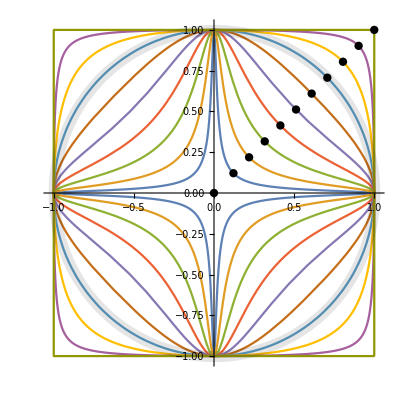

```mathematica
ParametricPlot[Table[
E^(I ϕ)√(2/(1+√(1+(1/k^4-2/k^2) Sin[2 ϕ]^2))),{k,-2+3/(√2),1,1/6 (2-√2)}]//ReIm//Evaluate
,{ϕ,0,2Pi},PlotRange->{-1.02,1.02},PlotPoints->30,GridLines->{(Range[40]-20)/10,(Range[40]-20)/10},
Epilog->{
{Black,Thickness[0.02],Opacity[0.1],Circle[{0,0},1]},
{PointSize[0.015],Point[{0,0}],Point[Table[{k,k},{k,-2+3/(√2),1,1/6 (2-√2)}]]}
}
]//Quiet
```

Вы также можете обратить внимание, что в этой формуле нет таких хитростей, как функции остатка от деления, взятия/отбрасывания знака и прочего - как это требуется для суперэллипса. Всё честно, только стандартные математические функции, с которыми не возникнет сложности при дифференцировании или интегрировании. Кстати про интегрирование - при желании , можно найти и площадь этих фигур (через эллиптические интегралы):

```mathematica
(4 k^4 EllipticE[(-1+2 k^2)/k^4]-4 (-1+k^2)^2 EllipticK[(-1+2 k^2)/k^4])/(-1+2 k^2)
```

(4 k^4 EllipticE[(-1+2 k^2)/k^4]-4 (-1+k^2)^2 EllipticK[(-1+2 k^2)/k^4])/(-1+2 k^2)

[Примечание] Эллиптические интегралы - это такие же функции, как и все остальные, вроде sin и cos. Похожее на операцию взятия первообразной название не должно вводить вас в заблуждение.

## Развитие

Можно добавить больше вариативности полученным фигурам. Например, так:

```mathematica
ρ=√((1+√((-2+z)^2/z^2))/(1+√(1+((4 (1-z))/z^2)Cos[2 ϕ]^2+(1/k^4-2/k^2) Sin[2 ϕ]^2)))
```

Здесь у нас появился ещё один параметр z, позволяющий искажать фигуру не нарушая идеологию построения. С её помощью можно приблизить нашу фигуру к суперэллипсу. Например, при n=4 совпадение почти идеальное (k=0.266, z=0.1):

```mathematica
Manipulate[
ParametricPlot[{
Sign[Cos[ϕ]] Abs[Cos[ϕ]]^(2/n)+I Sign[Sin[ϕ]] Abs[Sin[ϕ]]^(2/n)/.n->4,
E^(I ϕ)√((1+√((-2+z)^2/z^2))/(1+√(1+((4 (1-z))/z^2)Cos[2 ϕ]^2+(1/k^4-2/k^2) Sin[2 ϕ]^2)))
}//ReIm//Evaluate
,{ϕ,0,2Pi },GridLines->{(Range[40]-20)/10,(Range[40]-20)/10},PlotStyle->{{Thickness[0.03],Opacity[0.3],Hue[0.15, 1, 0.75]},{Thick,Hue[0.63, 1, 0.64]}},Exclusions->None]
,{{k,0.266},0.1,1},{{z,0.1},0.01,2}]
```

при более высоких n разница уже более ощутима (n=5, k=0.6, z=0.48):

```mathematica
Manipulate[
ParametricPlot[{
Sign[Cos[ϕ]] Abs[Cos[ϕ]]^(2/n)+I Sign[Sin[ϕ]] Abs[Sin[ϕ]]^(2/n)/.n->5,
E^(I ϕ)√((1+√((-2+z)^2/z^2))/(1+√(1+((4 (1-z))/z^2)Cos[2 ϕ]^2+(1/k^4-2/k^2) Sin[2 ϕ]^2)))
}//ReIm//Evaluate
,{ϕ,0,2Pi },GridLines->{(Range[40]-20)/10,(Range[40]-20)/10},PlotStyle->{{Thickness[0.03],Opacity[0.3],Hue[0.15, 1, 0.75]},{Thick,Hue[0.63, 1, 0.64]}},Exclusions->None]
,{{k,0.6},0.1,1},{{z,0.48},0.3,2}]
```

n=10 (k=0.942, z=1.02):

```mathematica
Manipulate[
ParametricPlot[{
Sign[Cos[ϕ]] Abs[Cos[ϕ]]^(2/n)+I Sign[Sin[ϕ]] Abs[Sin[ϕ]]^(2/n)/.n->10,
E^(I ϕ)√((1+√((-2+z)^2/z^2))/(1+√(1+((4 (1-z))/z^2)Cos[2 ϕ]^2+(1/k^4-2/k^2) Sin[2 ϕ]^2)))
}//ReIm//Evaluate
,{ϕ,0,2Pi },GridLines->{(Range[40]-20)/10,(Range[40]-20)/10},PlotStyle->{{Thickness[0.03],Opacity[0.3],Hue[0.15, 1, 0.75]},{Thick,Hue[0.63, 1, 0.64]}},Exclusions->None]
,{{k,0.942},0.1,1},{{z,1.02},0.3,2}]
```

И да, можно же пойти совсем радикальным способом! Такой дизайн иконок уж точно ни с чем не перепутаешь:

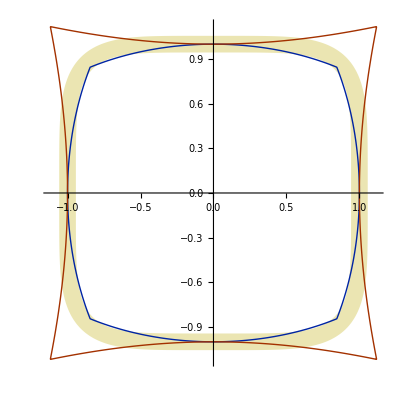

```mathematica
ParametricPlot[{
Sign[Cos[ϕ]] Abs[Cos[ϕ]]^(2/n)+I Sign[Sin[ϕ]] Abs[Sin[ϕ]]^(2/n)/.n->5,
E^(I ϕ)√((1+√((-2+z)^2/z^2))/(1+√(((-2+z)^2 Cos[2 ϕ]^2)/z^2)))/.z->1.4,
E^(I ϕ)√((1+√((-2+z)^2/z^2))/(1+√(((-2+z)^2 Cos[2 ϕ]^2)/z^2)))/.z->0.8
}//ReIm//Evaluate
,{ϕ,0,2Pi },GridLines->{(Range[40]-20)/10,(Range[40]-20)/10},PlotStyle->{{Thickness[0.03],Opacity[0.3],Hue[0.15, 1, 0.75]},{Thick,Hue[0.63, 1, 0.64]},{Thick,Hue[0.05, 1, 0.64]}},Exclusions->None]
```

Ну и с анимацией тоже можно слегка пофантазировать:

```mathematica
Animate[ParametricPlot[{
E^(I ϕ)√((1+√((-2+z)^2/z^2))/(1+√(1+((4 (1-z))/z^2)Cos[2 ϕ]^2+(1/k^4-2/k^2) Sin[2 ϕ]^2)))/.{z->1+Cos[a]/2,k->1-Sin[a]0.95}
}//ReIm//Evaluate
,{ϕ,0,2Pi },PlotRange->{-1.5,1.5},PlotPoints->100,GridLines->{(Range[40]-20)/10,(Range[40]-20)/10},PlotStyle->{{Thick,Hue[0.63, 1, 0.64]},{Thick,Hue[0.05, 1, 0.64]}},Exclusions->None],{a,-Pi,Pi}]
```

## Заключение

Если некий дизайнер некоторой фирмы с (необязательно) фруктовым логотипом хочет получить уникальный дизайн, пусть и не отличающийся принципиально от уже существующих решений - возможно, стоит попробовать поискать [и запатентовать] действительно новую формулу, а не привлекать давно известное решение, навешивая на него тонны маркетингового булшита. Особенно если это может сделать just for fun простой человек из глубинки без специального образования.